```mathematica
AlgoList4[start_, end_, primes_] := AlgoList4[start, end, primes]=Module[{result, current,  maxdist, hops,distances},
result = 0;
current=start;
hops=0;
Monitor[
While[current ≤ end,
(*Print[current];*)
hops++;
distances=ParallelTable[Distance[current, p], {p, primes}];
maxdist = Max[distances];
If[maxdist==0,
result+=1;
current +=Max[Min[ParallelTable[Distance[current+1, p], {p, primes}]],1];
,
current += maxdist;
];
],
{primes,hops, result,N[Log[10,current]]}
];
Return [{primes,result,hops}];
]
```

```mathematica
values=With[
{step=1, base=10},
Table[
With[
{a=Timing[{exp,exp+step,AlgoList4[base^exp,base^(exp+step),{3,5,7,11}]}]},
(*Print[a];Last[Last[Last[a]]]*)Last[Last[Last[a]]]],
{exp,0,77777,step}
]
]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

{5,6,6,15,18,6,7,15,7,4,14,26,7,5,7,6,11,10,7,6,5,14,15,5,7,5,16,5,24,7,5,9,10,11,10,11,5,4,5,12,18,6,5,15,16,7,7,5,12,8,11,12,12,5,8,8,20,4,28,5,5,6,13,9,6,6,8,8,16,11,9,4,9,28,21,10,22,5,6,9,7,19,4,7,16,9,5,6,8,6,5,12,5,13,5,8,9,10,11,20,14,6,32,16,7,6,15,6,7,14,8,5,7,13,9,5,18,7,10,4,21,7,5,6,14,14,5,5,6,14,14,5,7,21,6,6,8,9,6,9,6,23,7,10,7,6,5,15,6,12,20,8,6,9,45,16,7,12,6,16,9,23,5,11,4,12,7,6,5,10,11,5,6,10,19,7,7,42,14,5,11,15,5,8,6,6,24,6,8,6,6,6,9,6,5,6,6,9,8,«77380»,6,11,9,7,10,21,6,5,18,23,8,6,19,9,5,27,5,5,4,6,9,10,6,12,6,9,6,14,5,11,10,17,9,17,8,12,5,6,7,10,5,6,6,8,18,19,6,5,14,7,8,7,8,7,8,18,13,7,5,5,8,9,7,6,7,6,11,13,5,7,6,6,21,8,10,16,5,6,28,6,6,4,21,21,6,16,15,6,5,12,12,8,5,10,9,5,12,6,5,6,6,11,14,5,6,8,13,6,11,5,7,7,7,10,16,5,6,9,9,8,15,5,8,35,6,11,10,7,7,14,7,8,34,44,15,6,5,16,9,6,6,14,22,5,9,6,12,11,21,5,6,16,31,21,5,14,6,6,8,10,5,6,7,6,12,5,6,17,19,4,12,14,6,18,8,19,6,13,8,20,14,6,10,17,5,25,7,19,8,7,9,13,15,12,6,11,5,9,6}

```mathematica
Export["c:\\temp\values1.txt",values]
```

c:\temp\values1.txt

```mathematica
lim =1  * N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]]
```

9.82444

```mathematica
N[Mean[values]]
```

10.4347

```mathematica
N[Kurtosis[values]]
```

20.9575

```mathematica
N[Skewness[values]]
```

3.20287

```mathematica
{1,2}-1
```

{0,1}

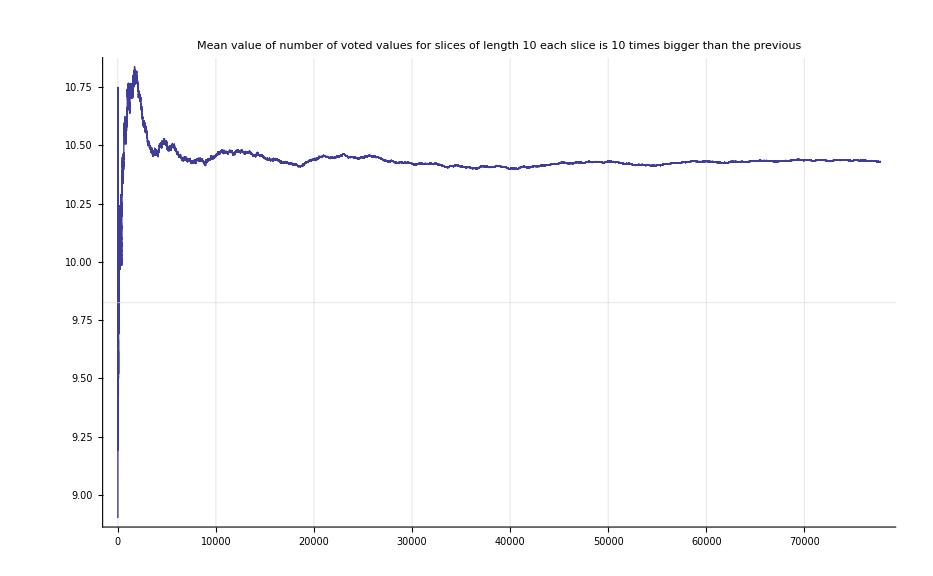

```mathematica
Monitor[ListPlot[Table[Mean[Take[values,i]],{i,10,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}},PlotLabel->"Mean value of number of voted values for slices of length 10\neach slice is 10 times bigger than the previous"],i]
```

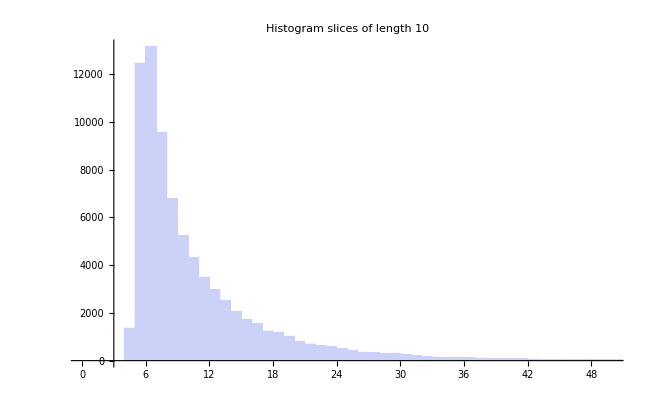

```mathematica
Histogram[values, PlotRange->{{0,50},Automatic},PlotLabel->"Histogram\nslices of length 10"]
```

```mathematica
FindFit[values,ChiSquareDistribution[ν],{v},x]
```

FindFit::nrlnum: The function value {-5.` + ChiSquareDistribution[ν], -6.` + ChiSquareDistribution[ν], -6.` + ChiSquareDistribution[ν], -15.` + ChiSquareDistribution[ν], -18.` + ChiSquareDistribution[ν], -6.` + ChiSquareDistribution[ν], -7.` + ChiSquareDistribution[ν], -15.` + ChiSquareDistribution[ν], -7.` + ChiSquareDistribution[ν], -4.` + ChiSquareDistribution[ν], « 65391 »} is not a list of real numbers with dimensions {65401} at {v} = {1.`}.

FindFit[{5,6,6,15,18,6,7,15,7,4,14,26,7,5,7,6,11,10,7,6,5,14,15,5,7,5,16,5,24,7,5,9,10,11,10,11,5,4,5,12,18,6,5,15,16,7,7,5,12,8,11,12,12,5,8,8,20,4,28,5,5,6,13,9,6,6,8,8,16,11,9,4,9,28,21,10,22,5,6,9,7,19,4,7,16,9,5,6,8,6,5,12,5,13,5,8,9,10,11,20,14,6,32,16,7,6,15,6,7,14,8,5,7,13,9,5,18,7,10,4,21,7,5,6,14,14,5,5,6,14,14,5,7,21,6,6,8,9,6,9,6,23,7,10,7,6,5,15,6,12,20,8,6,9,45,16,7,12,6,16,9,23,5,11,4,12,7,6,5,10,11,5,6,10,19,7,7,42,14,5,11,15,5,8,6,6,24,6,8,6,6,6,9,6,5,6,«65010»,10,7,5,6,6,6,25,5,5,11,10,6,8,13,6,8,7,9,5,13,5,8,7,16,11,14,5,11,8,10,4,7,7,8,8,16,10,13,6,10,7,9,11,27,5,13,12,6,5,7,14,13,6,11,7,18,7,32,8,5,7,11,18,7,24,5,6,6,13,16,5,5,7,13,4,8,5,11,23,23,7,8,11,20,10,47,8,17,5,7,8,14,11,7,20,5,12,14,9,13,60,9,26,8,12,7,5,5,15,6,6,5,10,8,7,11,5,6,6,4,8,13,7,6,56,5,13,5,8,6,10,7,7,6,14,8,5,10,46,11,5,9,38,8,8,36,5,7,5,21,6,11,5,8,20,5,6,5,12,14,6,7,7,5,7,13,11,5,6,6,7,9,12,7,5,9,29,11,5,8,8,5,14,7,12,10,18,7,5,9,6,6,10,19,15},«3»]

```mathematica
Min[values]
```

4

```mathematica
Max[values]
```

149

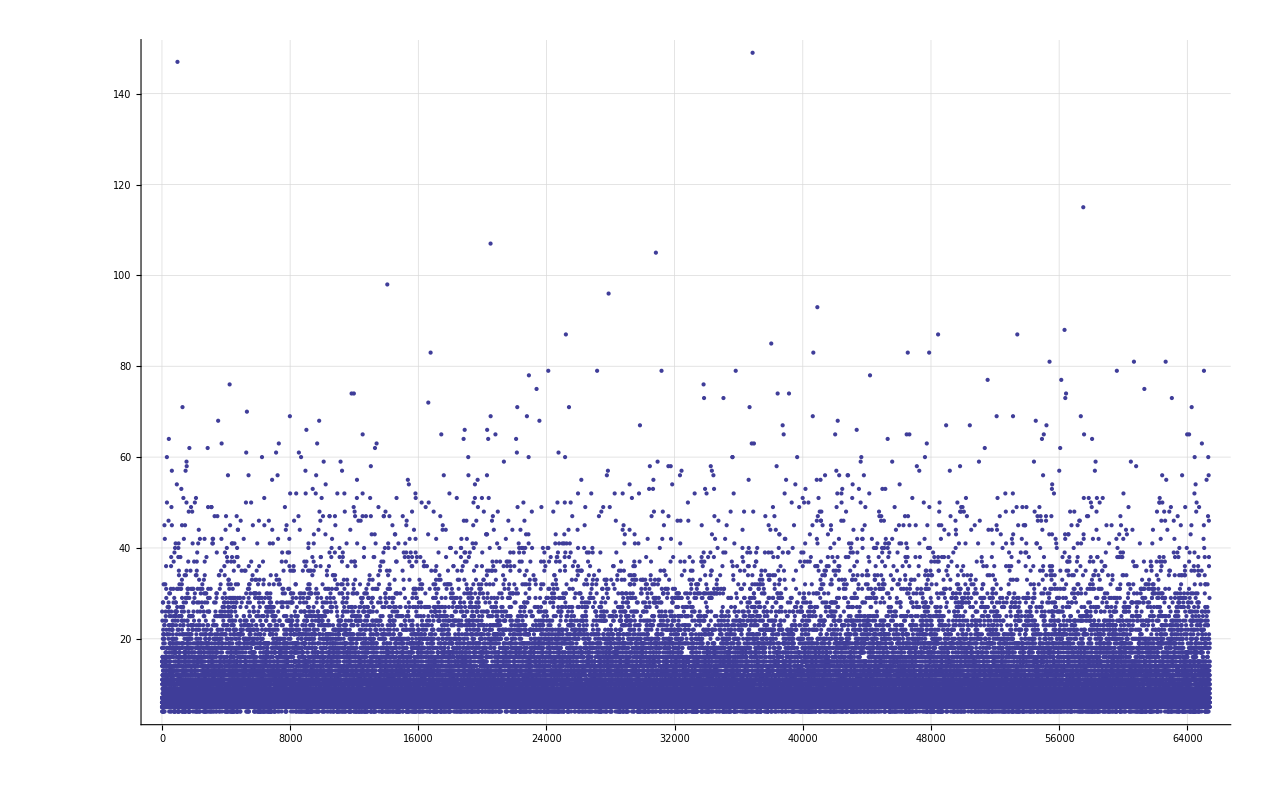

```mathematica
ListPlot[values,Joined->False,GridLines->Automatic,PlotRange->All]
```

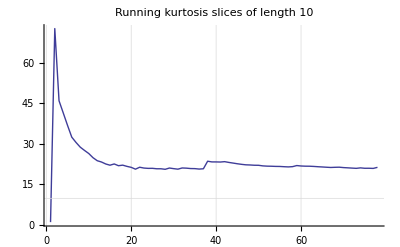

```mathematica
Monitor[ListPlot[Table[Kurtosis[Take[values,i]],{i,2,Length[values],1000}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}},PlotLabel->"Running kurtosis\nslices of length 10"],i]
```

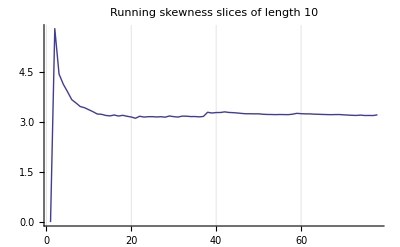

```mathematica
Monitor[ListPlot[Table[Skewness[Take[values,i]],{i,2,Length[values],1000}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}},PlotLabel->"Running skewness\nslices of length 10"],i]
```